```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes"]
```

C:\Users\pglpm\repositories\genobayes

```mathematica
NS["multinomial_coeffs"]
```

```mathematica
sum3[nn_,a1_,a2_,a3_]:=Sum[aa0=nn-aa1-aa2;Binomial[aa1,a1]*Binomial[aa2,a2]*Binomial[aa0,a3],{aa1,0,nn},{aa2,0,nn-aa1}];
sum4[nn_,a1_,a2_,a3_,a4_]:=Sum[aa0=nn-aa1-aa2-aa3;Binomial[aa1,a1]*Binomial[aa2,a2]*Binomial[aa3,a3]*Binomial[aa0,a4],{aa1,0,nn},{aa2,0,nn-aa1},{aa3,0,nn-aa1-aa2}];
```

```mathematica
tests3[nn_,a1_,a2_,a3_]:=Binomial[nn+3-1,a1+a2+a3+3-1];
tests4[nn_,a1_,a2_,a3_,a4_]:=Binomial[nn+4-1,a1+a2+a3+a4+4-1];
```

```mathematica
Through[{sum3,tests3}[10,2,1,4]]
```

{220,220}

```mathematica
Through[{sum4,tests4}[20,3,1,5,2]]
```

{817190,817190}

```mathematica
exp3[nn_,a1_,a2_,a3_]:=Sum[aa0=nn-aa1-aa2;aa1/nn*Binomial[aa1,a1]*Binomial[aa2,a2]*Binomial[aa0,a3],{aa1,0,nn},{aa2,0,nn-aa1}];

exp4[nn_,a1_,a2_,a3_,a4_]:=Sum[aa0=nn-aa1-aa2-aa3;aa1/nn*Binomial[aa1,a1]*Binomial[aa2,a2]*Binomial[aa3,a3]*Binomial[aa0,a4],{aa1,0,nn},{aa2,0,nn-aa1},{aa3,0,nn-aa1-aa2}];
```

```mathematica
teste3[nn_,a1_,a2_,a3_]:=(a1+1)/nn*Binomial[nn+3,a1+a2+a3+3]-Binomial[nn+3-1,a1+a2+a3+3-1]/nn;

teste3b[nn_,a1_,a2_,a3_]:=(a1+1)*(Binomial[nn+3,a1+a2+a3+3])-Binomial[nn+3-1,a1+a2+a3+3-1];

teste4[nn_,a1_,a2_,a3_,a4_]:=(a1+1)/nn*Binomial[nn+4,a1+a2+a3+a4+4]-Binomial[nn+4-1,a1+a2+a3+a4+4-1]/nn;

teste4b[nn_,a1_,a2_,a3_,a4_]:=(a1+1)*(Binomial[nn+4,a1+a2+a3+a4+4])-Binomial[nn+4-1,a1+a2+a3+a4+4-1];
```

```mathematica
Through[{exp3,teste3}[10,1,3,3]]
```

{176/5,176/5}

```mathematica
Through[{exp4,teste4}[20,5,4,6,2]]
```

{10373/20,10373/20}

```mathematica
Binomial[0,3]
```

0

```mathematica
teste4[20,3,2,6,2]
```

9/68

```mathematica
data=Import["dataset1.csv","Table","FieldSeparators"->";"][[;;,Join[{1,4,5,6},Range[8,101]]]];
```

```mathematica
Dimensions[data]
```

{6030,98}

```mathematica
sym=4;
```

```mathematica
data[[1]]
```

{ï»¿IID,SEX,AGE,GROUP,rs697680_A,rs228729_T,rs11121023_A,rs10864315_T,rs170631_G,rs875994_C,rs228682_C,rs228666_C,rs228669_T,rs228688_T,rs228690_T,rs10462018_T,rs228692_A,rs697690_C,rs2640908_T,rs4663866_C,rs934945_T,rs2304669_C,rs10462023_A,rs11894491_A,rs13002160_T,rs10462028_A,rs1801260_G,rs3792603_G,rs11133383_C,rs11932595_G,rs13113518_C,rs900144_C,rs4414197_T,rs7950226_A,rs10832020_C,rs11022761_T,rs11022762_T,rs7126796_C,rs10766077_A,rs7924734_G,rs10832027_G,rs1026071_G,rs12421530_C,rs2290036_C,rs1868049_T,rs3789327_G,rs11022778_G,rs3816358_A,rs4757151_A,rs12363415_G,rs11022781_A,rs969485_G,rs11022783_A,rs17452383_G,rs7121611_T,rs7121775_C,rs2292913_A,rs11038698_C,rs11038699_G,rs2292910_A,rs3824872_A,rs17441402_T,rs703829_T,rs11171846_T,rs11171856_C,rs714359_A,rs12821586_A,rs11113153_T,rs3741892_C,rs10861688_T,rs12368868_G,rs2585408_T,rs2735611_G,rs3027178_G,rs3027171_A,rs2518023_T,rs3027160_C,rs4794826_T,rs883871_A,rs2102928_T,rs2071427_T,rs2269457_C,rs4795424_C,rrs2797687_T,rrs2794664_A,rrs228730_A,rrs228697_G,rrs6858749_T,rrs2412646_T,rrs11240_G,rrs2070062_C,rrs6486120_T,rrs5443_T,rrs7958822_A,rrs922270_C,rrs4964057_G,rrs11071547_T,rrs3848543_T}

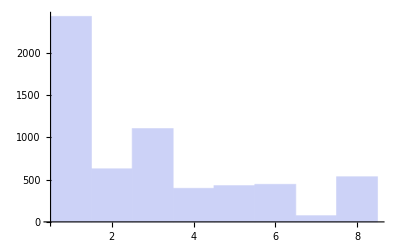

```mathematica
Histogram[data[[2;;,4]],PlotRange->All]
```

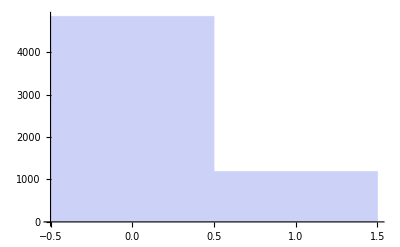

```mathematica
Histogram[data[[2;;,9]],PlotRange->All]
```

```mathematica
subd[gen_,val_]:=Pick[data,(#==val)&/@data[[;;,gen]],True]
```

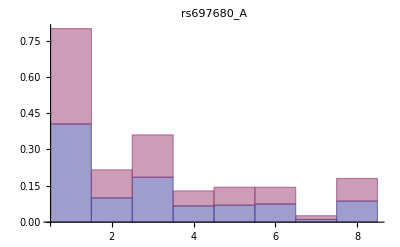
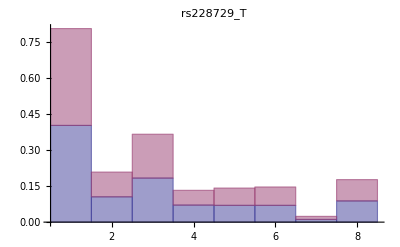

```mathematica
Table[Histogram[subd[var,#][[;;,sym]]&/@{0,1},Auto,"Probability",ChartLayout->"Stacked",PlotLabel->mystyle[data[[1,var]]]],{var,5,6}]
```

```mathematica
applyhist[data_,label_]:=Block[{dat=Pick[data,Map[(Length[#]>0)&,data],True]},(BarChart[Last/@#//Transpose,PlotLabel->label,ChartLabels->{Range[1,8],Auto},ChartLegends->Placed[Length/@dat,Below],PlotRange->All(*,FrameLabel->{"symptom",None},Frame->{True,True,False,False}*)]
&@(HistogramList[#,{1,8,1},"Probability"]&/@dat))];
```

```mathematica
tdati=subd[5,#][[;;,sym]]&/@{0,1};
```

```mathematica
(Length/@tdati)>0
```

{4537,1492}>0

```mathematica
Map[(Length[#]>0)&,tdati]
```

{True,True}

```mathematica
Pick[tdati,Map[
```

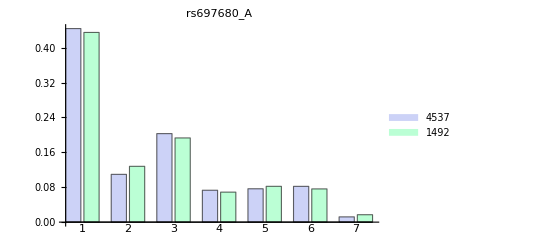

```mathematica
applyhist[subd[5,#][[;;,sym]]&/@{0,1},mystyle[data[[1,5]]]]
```

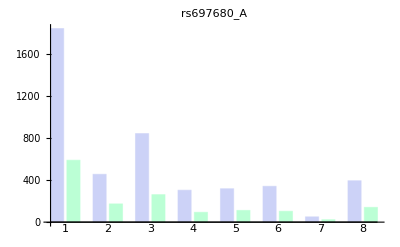
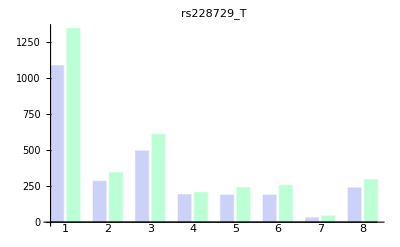

```mathematica
Table[applyhist[subd[var,#][[;;,sym]]&/@{0,1},mystyle[data[[1,var]]]],{var,5,6}]
```

```mathematica
tab=Table[Histogram[subd[var,#][[;;,sym]]&/@{0,1},Auto,"Probability",ChartLayout->"Stacked",PlotLabel->mystyle[data[[1,var]]]],{var,5,98}];
```

```mathematica
expdf0["test_sym_singlegene",Grid[ArrayReshape[tab,{10,10},""]]]
```

test_sym_singlegene.pdf

```mathematica
Tuples
```

```mathematica
Length/@(subd[var,#][[;;,sym]]&/@{{0,0},{0,1}})
```

{2695,3}

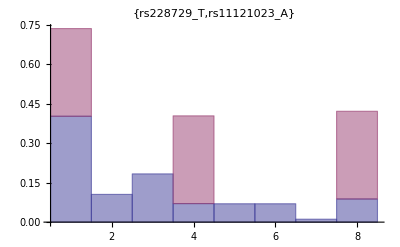

```mathematica
var={6,7};Histogram[subd[var,#][[;;,sym]]&/@{{0,0},{0,1}},Auto,"Probability",ChartLayout->"Stacked",PlotLabel->mystyle[data[[1,var]]]]
```

```mathematica
HistogramList[subd[var,#][[;;,sym]]&/@{{0,0},{0,1}},Auto,"Probability"]
```

```mathematica
HistogramList[subd[var,{0,1}][[;;,sym]],{1,8,1},"Probability"]
```

{{1,2,3,4,5,6,7,8},{0.5,0.,0.,0.5,0.,0.,0.}}

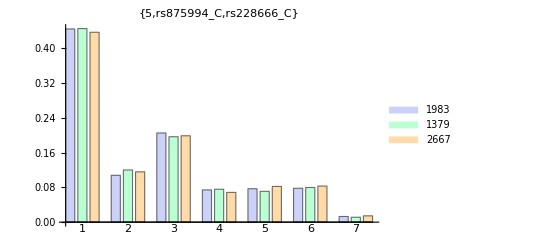

```mathematica
var=tuples[[42]];applyhist[subd[var,#][[;;,sym]]&/@Tuples[{0,1},2],mystyle[Join[{5},data[[1,var]]]]]
```

```mathematica
tuples=Subsets[Range[16,26],{2}];tab2=Table[var=tuples[[i]];applyhist[subd[var,#][[;;,sym]]&/@Tuples[{0,1},2],mystyle[Join[{i},data[[1,var]]]]],{i,Length@tuples}];
```

```mathematica
Sqrt@Length[tab2]//N
```

7.4162

```mathematica
expdf0["test_sym_2genesc",Grid[ArrayReshape[tab2,{8,8},""]]]
```

test_sym_2genesc.pdf

```mathematica
Length@Subsets[Range[5,98],{2}]
```

4371

```mathematica
ArrayReshape[Range[5,98],{10,10},""]
```

{{5,6,7,8,9,10,11,12,13,14},{15,16,17,18,19,20,21,22,23,24},{25,26,27,28,29,30,31,32,33,34},{35,36,37,38,39,40,41,42,43,44},{45,46,47,48,49,50,51,52,53,54},{55,56,57,58,59,60,61,62,63,64},{65,66,67,68,69,70,71,72,73,74},{75,76,77,78,79,80,81,82,83,84},{85,86,87,88,89,90,91,92,93,94},{95,96,97,98,,,,,,}}

```mathematica
Tuples
```

```mathematica
FactorInteger[%]
```

{{2,1},{47,1}}

```mathematica
Sqrt@%//N
```

9.69536

```mathematica
Pick
```

```mathematica
testd=data[[1;;10,1;;5]]
```

{{ï»¿IID,SEX,AGE,GROUP,rs697680_A},{1069170000202,1,54,3,1,0},{1069170000233,1,53,6,1,0},{1069170000318,1,79,9,1,0},{1069170000592,1,42,1,1,0},{1069170000622,1,38,6,1,1},{1069170000820,1,50,9,1,0},{1069170000967,2,44,3,1,1},{1069170001025,2,45,8,1,0},{1069170001421,2,35,1,0}}

```mathematica
Pick[testd,testd[[;;,5]],1]
```

{{1069170000622,1,38,6,1,1},{1069170000967,2,44,3,1,1}}

```mathematica
testd[[;;,{5}]]=={1}
```

False

```mathematica
(#=={1})&/@testd[[;;,{5}]]
```

{False,False,False,False,False,True,False,True,False,False}